# Solenoid Magnetic field

```mathematica
(* Vector potential *)
A=μ0/(4π)∫J[r]/Norm[x-r] ⅆr
(* B-field *)
B=μ0/(4π)∫ J[r]×((x-r)/Norm[x-r]^3)ⅆr
```

```mathematica
r=R{Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]};
x=X{Sin[α]Cos[β],Sin[α]Sin[β],Cos[α]};
x-r
(x-r).(x-r)//FullSimplify
```

{X Cos[β] Sin[α]-R Cos[ϕ] Sin[θ],X Sin[α] Sin[β]-R Sin[θ] Sin[ϕ],X Cos[α]-R Cos[θ]}

R^2+X^2-2 R X (Cos[α] Cos[θ]+Cos[β-ϕ] Sin[α] Sin[θ])

## Single Wire Loop by Legendre' s Polynomial

```mathematica
genK[l_,θ_]:=Integrate[LegendreP[l,Sin[θ]Cos[α]]Cos[α],{α,-π,π}]
StoreK=Table[genK[2n+1,ϕ],{n,0,9}];
K[n_,θ_]:=StoreK[[n+1]]/.{ϕ->θ}
```

```mathematica
Table[K[n,θ],{n,0,9}]
```

{π Sin[θ],-3/32 π (Sin[θ]+5 Sin[3 θ]),(15 π (2 Sin[θ]+7 (Sin[3 θ]+3 Sin[5 θ])))/1024,-(35 π (25 Sin[θ]+81 Sin[3 θ]+165 Sin[5 θ]+429 Sin[7 θ]))/65536,(315 π (98 Sin[θ]+11 (28 Sin[3 θ]+52 Sin[5 θ]+91 Sin[7 θ]+221 Sin[9 θ])))/4194304,-(693 π (882 Sin[θ]+13 (210 Sin[3 θ]+375 Sin[5 θ]+595 Sin[7 θ]+969 Sin[9 θ]+2261 Sin[11 θ])))/134217728,1/4294967296 3003 π (4356 Sin[θ]+13365 Sin[3 θ]+17 (1375 Sin[5 θ]+19 (110 Sin[7 θ]+162 Sin[9 θ]+253 Sin[11 θ]+575 Sin[13 θ]))),-1/549755813888 6435 π (184041 Sin[θ]+17 (33033 Sin[3 θ]+19 (3003 Sin[5 θ]+4459 Sin[7 θ]+23 (273 Sin[9 θ]+385 Sin[11 θ]+585 Sin[13 θ]+1305 Sin[15 θ])))),(109395 π Sin[θ])/32768-(2078505 π Sin[θ]^3)/16384+(101846745 π Sin[θ]^5)/65536-(2342475135 π Sin[θ]^7)/262144+(58561878375 π Sin[θ]^9)/2097152-(105411381075 π Sin[θ]^11)/2097152+(436704293025 π Sin[θ]^13)/8388608-(1933976154825 π Sin[θ]^15)/67108864+(7091245901025 π Sin[θ]^17)/1073741824,-(230945 π Sin[θ])/65536+(43648605 π Sin[θ]^3)/262144-(334639305 π Sin[θ]^5)/131072+(19520626125 π Sin[θ]^7)/1048576-(316234143225 π Sin[θ]^9)/4194304+(3056930051175 π Sin[θ]^11)/16777216-(4512611027925 π Sin[θ]^13)/16777216+(63821213109225 π Sin[θ]^15)/268435456-(248193606535875 π Sin[θ]^17)/2147483648+(204070298707275 π Sin[θ]^19)/8589934592}

```mathematica
genBext[n_,a_,r_,θ_]:=a^(2n+1)/r^(2n+3){(1/Sin[θ] D[Sin[θ]K[n,θ],θ]),(2n+1)K[n,θ]}
genBint[n_,a_,r_,θ_]:=r^(2n)/a^(2n+2){(1/Sin[θ] D[Sin[θ]K[n,θ],θ]),-(2n+2)K[n,θ]}
```

```mathematica
StoreBext=Table[genBext[n,b,p,ϕ],{n,0,9}];
Bext[n_,a_,r_,θ_]:=(StoreBext[[n+1]]/.{b->a,p->r,ϕ-> θ})//Simplify
StoreBint=Table[genBint[n,b,p,ϕ],{n,0,9}];
Bint[n_,a_,r_,θ_]:=(StoreBint[[n+1]]/.{b->a,p->r,ϕ-> θ})//Simplify
```

```mathematica
Bint[0,a,r,θ]
Bint[1,a,r,θ]
Bint[2,a,r,θ]
```

{(2 π Cos[θ])/a^2,-(2 π Sin[θ])/a^2}

{-(3 π r^2 (3 Cos[θ]+5 Cos[3 θ]))/(8 a^4),(3 π r^2 (Sin[θ]+5 Sin[3 θ]))/(8 a^4)}

{(15 π r^4 (30 Cos[θ]+35 Cos[3 θ]+63 Cos[5 θ]))/(512 a^6),-(45 π r^4 (2 Sin[θ]+7 (Sin[3 θ]+3 Sin[5 θ])))/(512 a^6)}

```mathematica
(* covert to rentangular coordiante *)
genBextRec[n_,a_,X_,Z_]:=Bext[n,a,√(X^2+Z^2),ArcSin[X/(√(X^2+Z^2))]][[1]]{X/(√(X^2+Z^2)),Z/(√(X^2+Z^2))}+Bext[n,a,√(X^2+Z^2),ArcSin[X/(√(X^2+Z^2))]][[2]]{Z/(√(X^2+Z^2)),-X/(√(X^2+Z^2))}
genBintRec[n_,a_,X_,Z_]:=Bint[n,a,√(X^2+Z^2),ArcSin[X/(√(X^2+Z^2))]][[1]]{X/(√(X^2+Z^2)),Z/(√(X^2+Z^2))}+Bint[n,a,√(X^2+Z^2),ArcSin[X/(√(X^2+Z^2))]][[2]]{Z/(√(X^2+Z^2)),-X/(√(X^2+Z^2))}
StoreBextRec=FullSimplify[Table[genBextRec[n,b,p,q],{n,0,9}],{p^2+q^2>0,q>0}]
BextRec[n_,a_,X_,Z_]:=StoreBextRec[[n+1]]/.{b->a,p->X,q->Z}
StoreBintRec=FullSimplify[Table[genBintRec[n,b,p,q],{n,0,9}],{p^2+q^2>0,q>0}]
BintRec[n_,a_,X_,Z_]:=StoreBintRec[[n+1]]/.{b->a,p->X,q->Z}
```

{{(3 b p π q)/((p^2+q^2)^(5/2)),-(b π (p^2-2 q^2))/((p^2+q^2)^(5/2))},{(15 b^3 p π q (3 p^2-4 q^2))/(8 (p^2+q^2)^(9/2)),-(3 b^3 π (3 p^4-24 p^2 q^2+8 q^4))/(8 (p^2+q^2)^(9/2))},{(105 b^5 p π (5 p^4 q-20 p^2 q^3+8 q^5))/(64 (p^2+q^2)^(13/2)),(15 b^5 π (-5 p^6+90 p^4 q^2-120 p^2 q^4+16 q^6))/(64 (p^2+q^2)^(13/2))},{(315 b^7 π (35 p^7 q-280 p^5 q^3+336 p^3 q^5-64 p q^7))/(1024 (p^2+q^2)^(17/2)),-(35 b^7 π (35 p^8-1120 p^6 q^2+3360 p^4 q^4-1792 p^2 q^6+128 q^8))/(1024 (p^2+q^2)^(17/2))},{(3465 b^9 p π (63 p^8 q-840 p^6 q^3+2016 p^4 q^5-1152 p^2 q^7+128 q^9))/(16384 (p^2+q^2)^(21/2)),(315 b^9 π (-63 p^10+3150 p^8 q^2-16800 p^6 q^4+20160 p^4 q^6-5760 p^2 q^8+256 q^10))/(16384 (p^2+q^2)^(21/2))},{(9009 b^11 π (231 p^11 q-4620 p^9 q^3+18480 p^7 q^5-21120 p^5 q^7+7040 p^3 q^9-512 p q^11))/(131072 (p^2+q^2)^(25/2)),-(693 b^11 π (231 p^12-16632 p^10 q^2+138600 p^8 q^4-295680 p^6 q^6+190080 p^4 q^8-33792 p^2 q^10+1024 q^12))/(131072 (p^2+q^2)^(25/2))},{(45045 b^13 p π (429 p^12 q-12012 p^10 q^3+72072 p^8 q^5-137280 p^6 q^7+91520 p^4 q^9-19968 p^2 q^11+1024 q^13))/(1048576 (p^2+q^2)^(29/2)),1/(1048576 (p^2+q^2)^(29/2))3003 b^13 π (-429 p^14+42042 p^12 q^2-504504 p^10 q^4+1681680 p^8 q^6-1921920 p^6 q^8+768768 p^4 q^10-93184 p^2 q^12+2048 q^14)},{1/(33554432 (p^2+q^2)^(33/2))109395 b^15 π (6435 p^15 q-240240 p^13 q^3+2018016 p^11 q^5-5765760 p^9 q^7+6406400 p^7 q^9-2795520 p^5 q^11+430080 p^3 q^13-16384 p q^15),-1/(33554432 (p^2+q^2)^(33/2))6435 b^15 π (6435 p^16-823680 p^14 q^2+13453440 p^12 q^4-64576512 p^10 q^6+115315200 p^8 q^8-82001920 p^6 q^10+22364160 p^4 q^12-1966080 p^2 q^14+32768 q^16)},{1/(1073741824 (p^2+q^2)^(37/2))2078505 b^17 p π (12155 p^16 q-583440 p^14 q^3+6534528 p^12 q^5-26138112 p^10 q^7+43563520 p^8 q^9-31682560 p^6 q^11+9748480 p^4 q^13-1114112 p^2 q^15+32768 q^17),1/(1073741824 (p^2+q^2)^(37/2))109395 b^17 π (-12155 p^18+1969110 p^16 q^2-42007680 p^14 q^4+274450176 p^12 q^6-705729024 p^10 q^8+784143360 p^8 q^10-380190720 p^6 q^12+75202560 p^4 q^14-5013504 p^2 q^16+65536 q^18)},{1/(8589934592 (p^2+q^2)^(41/2))4849845 b^19 p π (46189 p^18 q-2771340 p^16 q^3+39907296 p^14 q^5-212838912 p^12 q^7+496624128 p^10 q^9-541771776 p^8 q^11+277831680 p^6 q^13-63504384 p^4 q^15+5603328 p^2 q^17-131072 q^19),-1/(8589934592 (p^2+q^2)^(41/2))230945 b^19 π (46189 p^20-9237800 p^18 q^2+249420600 p^16 q^4-2128389120 p^14 q^6+7449361920 p^12 q^8-11918979072 p^10 q^10+9029529600 p^8 q^12-3175219200 p^6 q^14+476282880 p^4 q^16-24903680 p^2 q^18+262144 q^20)}}

{{0,(2 π)/b^2},{(3 p π q)/b^4,(3 π (p^2-2 q^2))/(2 b^4)},{(15 p π (3 p^2 q-4 q^3))/(8 b^6),(15 π (3 p^4-24 p^2 q^2+8 q^4))/(32 b^6)},{(105 p π (5 p^4 q-20 p^2 q^3+8 q^5))/(64 b^8),(35 π (5 p^6-90 p^4 q^2+120 p^2 q^4-16 q^6))/(128 b^8)},{(315 p π (35 p^6 q-280 p^4 q^3+336 p^2 q^5-64 q^7))/(1024 b^10),(315 π (35 p^8-1120 p^6 q^2+3360 p^4 q^4-1792 p^2 q^6+128 q^8))/(8192 b^10)},{(3465 p π (63 p^8 q-840 p^6 q^3+2016 p^4 q^5-1152 p^2 q^7+128 q^9))/(16384 b^12),(693 π (63 p^10-3150 p^8 q^2+16800 p^6 q^4-20160 p^4 q^6+5760 p^2 q^8-256 q^10))/(32768 b^12)},{(9009 p π (231 p^10 q-4620 p^8 q^3+18480 p^6 q^5-21120 p^4 q^7+7040 p^2 q^9-512 q^11))/(131072 b^14),(3003 π (231 p^12-16632 p^10 q^2+138600 p^8 q^4-295680 p^6 q^6+190080 p^4 q^8-33792 p^2 q^10+1024 q^12))/(524288 b^14)},{(45045 p π (429 p^12 q-12012 p^10 q^3+72072 p^8 q^5-137280 p^6 q^7+91520 p^4 q^9-19968 p^2 q^11+1024 q^13))/(1048576 b^16),1/(2097152 b^16)6435 π (429 p^14-42042 p^12 q^2+504504 p^10 q^4-1681680 p^8 q^6+1921920 p^6 q^8-768768 p^4 q^10+93184 p^2 q^12-2048 q^14)},{1/(33554432 b^18)109395 p π q (6435 p^14-240240 p^12 q^2+2018016 p^10 q^4-5765760 p^8 q^6+6406400 p^6 q^8-2795520 p^4 q^10+430080 p^2 q^12-16384 q^14),1/(536870912 b^18)109395 π (6435 p^16-823680 p^14 q^2+13453440 p^12 q^4-64576512 p^10 q^6+115315200 p^8 q^8-82001920 p^6 q^10+22364160 p^4 q^12-1966080 p^2 q^14+32768 q^16)},{1/(1073741824 b^20)2078505 p π q (12155 p^16-583440 p^14 q^2+6534528 p^12 q^4-26138112 p^10 q^6+43563520 p^8 q^8-31682560 p^6 q^10+9748480 p^4 q^12-1114112 p^2 q^14+32768 q^16),1/(2147483648 b^20)230945 π (12155 p^18-1969110 p^16 q^2+42007680 p^14 q^4-274450176 p^12 q^6+705729024 p^10 q^8-784143360 p^8 q^10+380190720 p^6 q^12-75202560 p^4 q^14+5013504 p^2 q^16-65536 q^18)}}

```mathematica
SumBextRec[m_,a_,X_,Z_]:=Sum[BextRec[n,a,X,Z],{n,0,m}]
SumBintRec[m_,a_,X_,Z_]:=Sum[BintRec[n,a,X,Z],{n,0,m}]
```

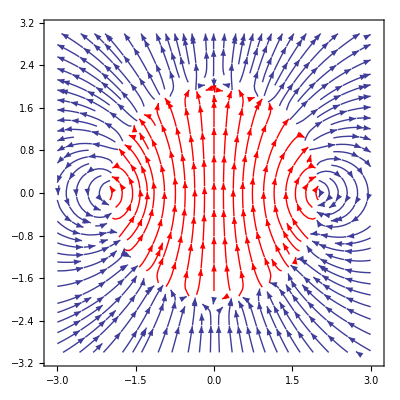

```mathematica
Show[
StreamPlot[SumBextRec[9,2,X,Z],{X,-3,3},{Z,-3,3},StreamPoints->Fine,RegionFunction->Function[{X,Z},X^2+Z^2>4]],
StreamPlot[SumBintRec[9,2,X,Z],{X,-3,3},{Z,-3,3},StreamPoints->Fine,StreamStyle->Red,RegionFunction->Function[{X,Z},X^2+Z^2<4]]
]
```

```mathematica
15/512//N
```

0.0292969

## Single Wire Loop by Elliptical integral

```mathematica
(*Current Density *)
Jϕ=i DiracDelta[z]DiracDelta[r-a]
J=i DiracDelta[z]DiracDelta[r-a]{-Sin[ϕ],Cos[ϕ],0}
```

```mathematica
(* For cylindrical symmetry, we set β=0*)
r={ρ,0,z};
x={a Cos[ϕ],a Sin[ϕ],0};
(x-r).(x-r)//Expand//FullSimplify
```

a^2+z^2+ρ^2-2 a ρ Cos[ϕ]

```mathematica
(* The volume integral of A *)
μ0/(4π)i∫ DiracDelta[z]DiracDelta[r-a]Cos[ϕ]rⅆr ⅆzⅆϕ
μ0/(4π)i a(∫_0^(2π) Cos[ϕ]/(√(a^2+z^2+ρ^2-2 a ρ Cos[ϕ]))ⅆϕ)
μ0/(2π)i a(∫_0^π Cos[ϕ]/(√(a^2+z^2+ρ^2-2 a ρ Cos[ϕ]))ⅆϕ)
1/(2π)a(∫_0^π Cos[ϕ]/(√(a^2+z^2+ρ^2-2 a ρ Cos[ϕ]))ⅆϕ)
```

```mathematica
Manipulate[Plot[Cos[ϕ]/(√(a^2+z^2+ρ^2-2 a ρ Cos[ϕ])),{ϕ,0,2π}],{a,0.5,1},{ρ,0,4},{z,-2,2}]
```

```mathematica
(* By vector potential *)
Integrate[1/(2π)a Cos[ϕ]/(√(a^2+z^2+ρ^2+2 a ρ Cos[ϕ])),ϕ]
```

(√((a^2+z^2+ρ^2+2 a ρ Cos[ϕ])/(a^2+z^2+2 a ρ+ρ^2)) ((a^2+z^2+2 a ρ+ρ^2) EllipticE[ϕ/2,(4 a ρ)/(a^2+z^2+2 a ρ+ρ^2)]-(a^2+z^2+ρ^2) EllipticF[ϕ/2,(4 a ρ)/(a^2+z^2+2 a ρ+ρ^2)]))/(2 π ρ √(a^2+z^2+ρ^2+2 a ρ Cos[ϕ]))

```mathematica
Aϕ[a_,ρ_,z_]:=(√((a+ρ)^2+z^2))/(4 π ρ)( EllipticE[(4 a ρ)/((a+ρ)^2+z^2)]-(a^2+z^2+ρ^2)/((a+ρ)^2+z^2) EllipticK[(4 a ρ)/((a+ρ)^2+z^2)])
```

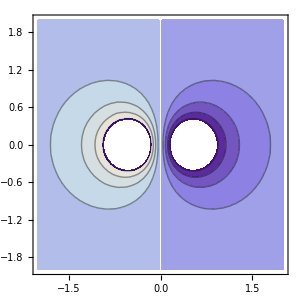

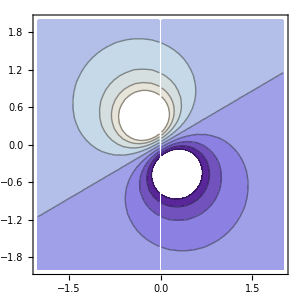

```mathematica
ContourPlot[Aϕ[0.5,R,Z],{R,-2,2},{Z,-2,2},ImageSize->300,Exclusions->{R==0}]
ContourPlot[Aϕ[0.5,R Cos[θ]-Z Sin[θ],R Sin[θ]+Z Cos[θ]]/.θ->π/3,{R,-2,2},{Z,-2,2},ImageSize->300,Exclusions->{R==0}]
```

```mathematica
(* magnetic field *)
(* For A = Aϕ *)
Br[a_,h_,k_,ρ_,z_]:=(z-k )/((ρ-h)  √((z-k )^2+(a+ρ-h)^2))((a^2+(z-k )^2+(ρ-h)^2)/((a-ρ+h)^2+(z-k )^2) EllipticE[(4 a (ρ-h))/((z-k )^2+(a+ρ-h)^2)]- EllipticK[(4 a(ρ-h))/((z-k )^2+(a+ρ-h)^2)])
Bz[a_,h_,k_,ρ_,z_]:=1/(√((z-k )^2+(a+ρ-h)^2))((a^2-(z-k )^2-(ρ-h)^2)/((a-ρ+h)^2+(z-k )^2) EllipticE[(4 a(ρ-h))/((z-k )^2+(a+ρ-h)^2)]+ EllipticK[(4 a (ρ-h))/((z-k )^2+(a+ρ-h)^2)])
```

```mathematica
Field[a_,h_,k_,θ_]:=StreamDensityPlot[Br[a,h,k,R Cos[θ]-Z Sin[θ],R Sin[θ]+Z Cos[θ]]{Cos[θ],-Sin[θ]}+Bz[a,h,k,R Cos[θ]-Z Sin[θ],R Sin[θ]+Z Cos[θ]]{Sin[θ],Cos[θ]},{R,-2,2},{Z,-2,2},StreamColorFunction->"Rainbow"]
```

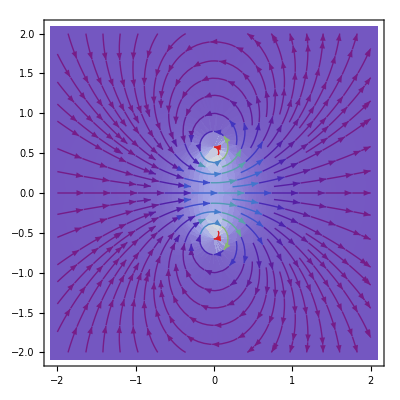

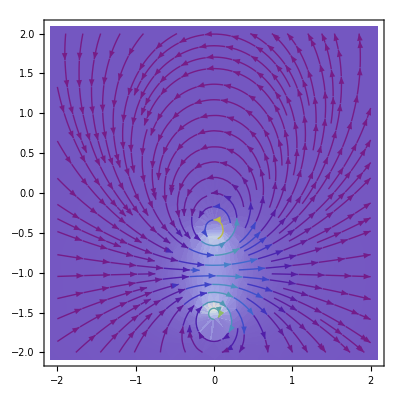

```mathematica
Field[0.5,0,0,π/2]
Field[0.5,1,0,π/2]
```

```mathematica
-Br[a,h,k,R Cos[θ]-Z Sin[θ],R Sin[θ]+Z Cos[θ]]Sin[θ]+Bz[a,h,k,R Cos[θ]-Z Sin[θ],R Sin[θ]+Z Cos[θ]]Cos[θ]//Simplify
```

(Cos[θ] (EllipticK[(4 a (-h+R Cos[θ]-Z Sin[θ]))/((-k+Z Cos[θ]+R Sin[θ])^2+(a-h+R Cos[θ]-Z Sin[θ])^2)]+(EllipticE[(4 a (-h+R Cos[θ]-Z Sin[θ]))/((-k+Z Cos[θ]+R Sin[θ])^2+(a-h+R Cos[θ]-Z Sin[θ])^2)] (a^2-(-k+Z Cos[θ]+R Sin[θ])^2-(h-R Cos[θ]+Z Sin[θ])^2))/((-k+Z Cos[θ]+R Sin[θ])^2+(a+h-R Cos[θ]+Z Sin[θ])^2))-1/(-h+R Cos[θ]-Z Sin[θ])Sin[θ] (-k+Z Cos[θ]+R Sin[θ]) (-EllipticK[(4 a (-h+R Cos[θ]-Z Sin[θ]))/((-k+Z Cos[θ]+R Sin[θ])^2+(a-h+R Cos[θ]-Z Sin[θ])^2)]+(EllipticE[(4 a (-h+R Cos[θ]-Z Sin[θ]))/((-k+Z Cos[θ]+R Sin[θ])^2+(a-h+R Cos[θ]-Z Sin[θ])^2)] (a^2+(-k+Z Cos[θ]+R Sin[θ])^2+(h-R Cos[θ]+Z Sin[θ])^2))/((-k+Z Cos[θ]+R Sin[θ])^2+(a+h-R Cos[θ]+Z Sin[θ])^2)))/(√((-k+Z Cos[θ]+R Sin[θ])^2+(a-h+R Cos[θ]-Z Sin[θ])^2))

```mathematica
(* here has a problem that the flux of a circle at center {h,k} is not symmetric *)
```

```mathematica
2π∫((Cos[θ] (EllipticK[(4 a (-h+R Cos[θ]-Z Sin[θ]))/((-k+Z Cos[θ]+R Sin[θ])^2+(a-h+R Cos[θ]-Z Sin[θ])^2)]+(EllipticE[(4 a (-h+R Cos[θ]-Z Sin[θ]))/((-k+Z Cos[θ]+R Sin[θ])^2+(a-h+R Cos[θ]-Z Sin[θ])^2)] (a^2-(-k+Z Cos[θ]+R Sin[θ])^2-(h-R Cos[θ]+Z Sin[θ])^2))/((-k+Z Cos[θ]+R Sin[θ])^2+(a+h-R Cos[θ]+Z Sin[θ])^2))-1/(-h+R Cos[θ]-Z Sin[θ])Sin[θ] (-k+Z Cos[θ]+R Sin[θ]) (-EllipticK[(4 a (-h+R Cos[θ]-Z Sin[θ]))/((-k+Z Cos[θ]+R Sin[θ])^2+(a-h+R Cos[θ]-Z Sin[θ])^2)]+(EllipticE[(4 a (-h+R Cos[θ]-Z Sin[θ]))/((-k+Z Cos[θ]+R Sin[θ])^2+(a-h+R Cos[θ]-Z Sin[θ])^2)] (a^2+(-k+Z Cos[θ]+R Sin[θ])^2+(h-R Cos[θ]+Z Sin[θ])^2))/((-k+Z Cos[θ]+R Sin[θ])^2+(a+h-R Cos[θ]+Z Sin[θ])^2)))/(√((-k+Z Cos[θ]+R Sin[θ])^2+(a-h+R Cos[θ]-Z Sin[θ])^2))R)ⅆR
```

$Aborted

```mathematica
Aϕ[a,R Cos[θ]-Z Sin[θ],R Sin[θ]+Z Cos[θ]]//Simplify
```

1/(4 π (R Cos[θ]-Z Sin[θ]))√(a^2+R^2+Z^2+2 a R Cos[θ]-2 a Z Sin[θ]) (EllipticE[(4 a (R Cos[θ]-Z Sin[θ]))/(a^2+R^2+Z^2+2 a R Cos[θ]-2 a Z Sin[θ])]-((a^2+R^2+Z^2) EllipticK[(4 a (R Cos[θ]-Z Sin[θ]))/(a^2+R^2+Z^2+2 a R Cos[θ]-2 a Z Sin[θ])])/(a^2+R^2+Z^2+2 a R Cos[θ]-2 a Z Sin[θ]))

## Current Disk

```mathematica
(* Current Density *)
Jϕ=((2i)/(b^2-a^2))DiracDelta[β-π/2]
```

```mathematica
∫_0^(2π) ∫_a^b DiracDelta[β-π/2]s ⅆsⅆβ
```

```mathematica
1/2 (-a^2+b^2)
```

```mathematica
J=Jϕ{-Sin[α],Cos[α],0}
```

```mathematica
(* position vector , with out loss of generality, ϕ=0*)
r=R{Sin[θ],0,Cos[θ]};
x={s Cos[α],s Sin[α],0};
r-x
(r-x).(r-x)//FullSimplify
```

{-s Cos[α]+R Sin[θ],-s Sin[α],R Cos[θ]}

R^2+s^2-2 R s Cos[α] Sin[θ]

```mathematica
(* Vector Potential *)
μ0/(4π)∫∫Jϕ sⅆsⅆα
```

## Magnetic field form a finite length wire ( Numerical Integral )

```mathematica
r={0,0,z};
x={X,Y,Z};
x-r
(x-r).(x-r)//FullSimplify
```

{X,Y,-z+Z}

X^2+Y^2+(z-Z)^2

```mathematica
(* Numerical *)
B[X_,Y_,Z_]:=NIntegrate[ ({0,0,1}×{X,Y,-z+Z})/((X^2+Y^2+(z-Z)^2)^(3/2)),{z,-0.5,0.5},AccuracyGoal-> 5,MinRecursion->4]
```

```mathematica
Norm[B[1,1,0]]
Norm[B[√2,0,0]]
```

0.471405

0.471405

```mathematica
XY=Table[Norm[B[X,Y,0]],{X,-1,1,0.05},{Y,-1,1,0.05}];
XZ=Table[Norm[B[X,0,Z]],{X,-1,1,0.05},{Z,-1,1,0.05}];
```

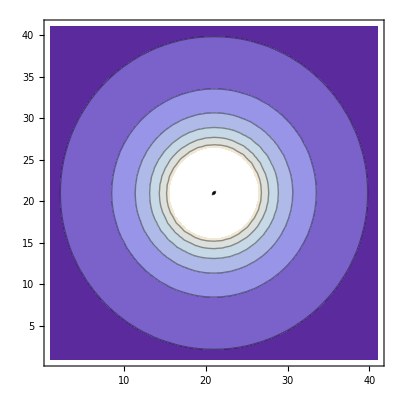

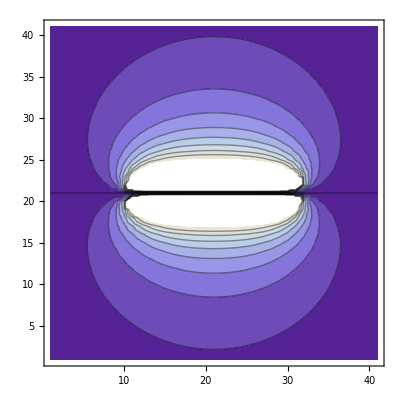

```mathematica
ListContourPlot[XY]
ListContourPlot[XZ]
```

## Striagth Line

```mathematica
r={0,0,z};
x={R Cos[ϕ],R Sin[ϕ],Z};
x-r
(x-r).(x-r)
```

{R Cos[ϕ],R Sin[ϕ],-z+Z}

(-z+Z)^2+R^2 Cos[ϕ]^2+R^2 Sin[ϕ]^2

```mathematica
Integrate[{0,0,1}/(√((-z+Z)^2+R^2 Cos[ϕ]^2+R^2 Sin[ϕ]^2)),z]
```

{0,0,Log[z+√(R^2+(z-Z)^2)-Z]}

```mathematica
({0,0,Log[z+√(R^2+(z-Z)^2)-Z]}/.z->L/2)-({0,0,Log[z+√(R^2+(z-Z)^2)-Z]}/.z->-L/2)//FullSimplify
```

{0,0,Log[L/2+√(R^2+1/4 (L-2 Z)^2)-Z]-Log[-L/2-Z+√(R^2+1/4 (L+2 Z)^2)]}

```mathematica
Az[R_,Z_,L_]:=Log[L/2+√(R^2+1/4 (L-2 Z)^2)-Z]-Log[-L/2-Z+√(R^2+1/4 (L+2 Z)^2)]
```

```mathematica
BR[R_,Z_,L_]:=Evaluate[1/R D[Az[R,Z,L],ϕ]//Expand]
Bϕ[R_,Z_,L_]:=Evaluate[-D[Az[R,Z,L],R]//Expand]
```

```mathematica
BR[R,Z,1]
Bϕ[R,Z,1]
```

0

-R/(√(R^2+1/4 (1-2 Z)^2) (1/2+√(R^2+1/4 (1-2 Z)^2)-Z))+R/(√(R^2+1/4 (1+2 Z)^2) (-1/2-Z+√(R^2+1/4 (1+2 Z)^2)))

```mathematica
Manipulate[StreamDensityPlot[Evaluate[Simplify[{-Bϕ[√(X^2+Y^2),Z,1] √(Y^2/(X^2+Y^2)),Bϕ[√(X^2+Y^2),Z,1] √(X^2/(X^2+Y^2))},{X^2+Y^2>0,X>0,Y>0}]],{X,-2,2},{Y,-2,2}],{Z,-2,2}]
```

```mathematica
VectorPlot3D[{(Y (4/(√((4 X^2+4 Y^2+(1-2 Z)^2)/(X^2+Y^2)) (1+√(4 X^2+4 Y^2+(1-2 Z)^2)-2 Z))-4/(√((4 X^2+4 Y^2+(1+2 Z)^2)/(X^2+Y^2)) (-1-2 Z+√(4 X^2+4 Y^2+(1+2 Z)^2)))))/(√(X^2+Y^2)),(X (-4/(√((4 X^2+4 Y^2+(1-2 Z)^2)/(X^2+Y^2)) (1+√(4 X^2+4 Y^2+(1-2 Z)^2)-2 Z))+4/(√((4 X^2+4 Y^2+(1+2 Z)^2)/(X^2+Y^2)) (-1-2 Z+√(4 X^2+4 Y^2+(1+2 Z)^2)))))/(√(X^2+Y^2)),0},{X,-2,2},{Y,-2,2},{Z,-2,2},VectorScale->0.2,VectorPoints->5]
```

-Graphics3D-